## Parameters

```mathematica
V[r_,α_,σ_,c_]:=c-α/r+σ r;
Vsb[r_,α_,σ_,c_]:=HeavisideTheta[rsb-r](c-α/r+σ r)+HeavisideTheta[r-rsb](c-α/rsb+σ rsb);
Veff[r_,l_,m_]:=(l(l+1))/(2m r^2);
(*from AR 1509.07366*)
σcont=0.415^2;
ccont=-0.176696;
αcont=0.50425;
mc=1.47164;
mb=4.882;
mbe=0.041;
μc=mc/2;
μb=mb/2;
(****)
```

```mathematica
rsb=r/.FindRoot[V[r,αcont,σcont,ccont]==8/10,{r,1}]
```

6.14733

```mathematica
rsb*0.197
```

1.21102

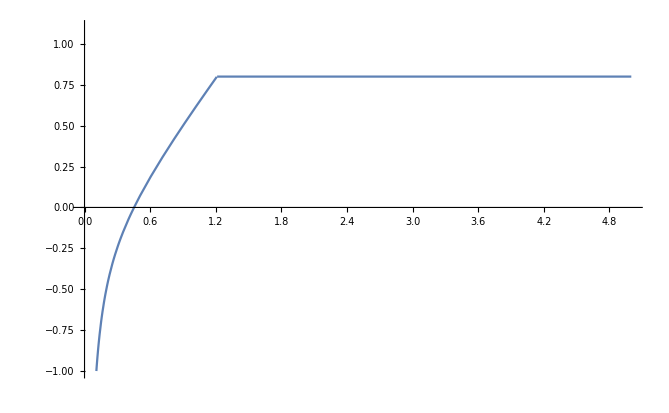

```mathematica
Plot[Vsb[r/0.197,αcont,σcont,ccont],{r,0,5},PlotRange->{-1,1.1}]
```

## Charmonium old

### Swave

```mathematica
{ccsvals,ccsvecs}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]+Vcont[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

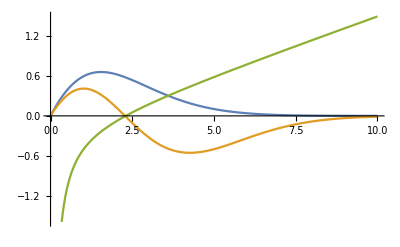

```mathematica
Plot[{ccsvecs[[1]][x],ccsvecs[[2]][x],Vcont[x]},{x,0,10}]
```

```mathematica
ccsvals
```

{0.152928,0.738566,1.16928,1.53686}

```mathematica
ccsmass=ConstantArray[2 mc,2]+Sort[ccsvals]
```

{3.09621,3.68185}

```mathematica
EMfactor=(ccsmass[[2]](ccsvecs[[1]][10^-100])/10^-100)^2/(ccsmass[[1]](ccsvecs[[2]][10^-100])/10^-100)^2
```

2.0689

```mathematica
{ccsvalsi,ccsvecsi}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]Exp[-2 ⅈ δ]+V[x Exp[ⅈ δ]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ccsvalsi
```

{0.152928+1.11666×10^-12 ⅈ,0.738566+1.70776×10^-12 ⅈ,1.16928+3.01912×10^-12 ⅈ,1.53686+8.25092×10^-13 ⅈ}

### Pwave

```mathematica
{ccpvals,ccpvecs}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]+V[x] u[x]+Veff[x,1,μc]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

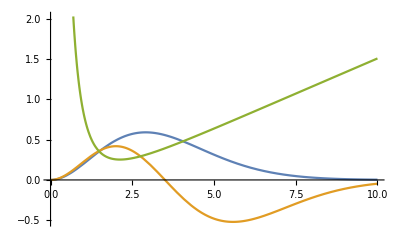

```mathematica
Plot[{ccpvecs[[1]][x],ccpvecs[[2]][x],V[x]+Veff[x,1,μc]},{x,0,10}]
```

```mathematica
ccpmass=ConstantArray[2 mc,2]+Sort[ccpvals][[;;2]]
```

{3.50904,3.96034}

## Bottomonium old

### Swave

```mathematica
{bbvals,bbvecs}=NDEigensystem[{-1/(2μb)Laplacian[u[x],{x}]+V[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

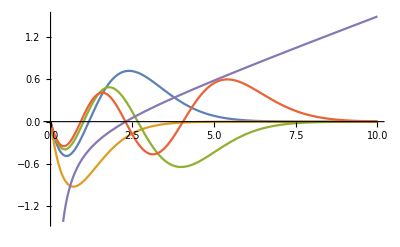

```mathematica
Plot[{bbvecs[[1]][x],bbvecs[[2]][x],bbvecs[[3]][x],bbvecs[[4]][x],V[x]},{x,0,10}]
```

```mathematica
bbmass=ConstantArray[2 mb,4]+Sort[bbvals][[;;4]]
```

{9.4599,10.019,10.3525,10.6217}

### Pwave

```mathematica
{bbpvals,bbpvecs}=NDEigensystem[{-1/(2μb)Laplacian[u[x],{x}]+V[x] u[x]+Veff[x,1,μb]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

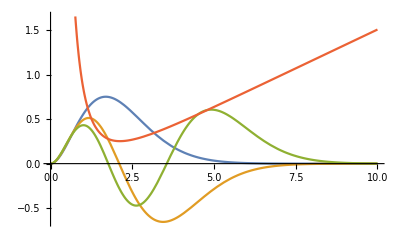

```mathematica
Plot[{bbpvecs[[1]][x],bbpvecs[[2]][x],bbpvecs[[3]][x],V[x]+Veff[x,1,μc]},{x,0,10}]
```

```mathematica
cbbpmass=ConstantArray[2 mb,3]+Sort[bbpvals]
```

{9.92524,10.2681,10.5432}

## New

### Bottomonium Fit

#### Parameter Calculation

```mathematica
Off[NDEigenvalues::femcnsd]
```

```mathematica
bbswavePDG={10.02326,9.4603,10.3552,10.5794};
bbswavePDGe={0.00031,0.00026,0.0002,0.0012};
bbswavePDG3={10.02326,9.4603,10.3552};
bbswavePDG3e={{10.02326,0.00031},{9.4603,0.00026},{10.3552,0.0002}};
bbpwavePDG={9.88814,10.252,10.534};
```

```mathematica
mbrand:=RandomVariate[NormalDistribution[mb,mbe]];
bbswavePDG3rand:={RandomVariate[NormalDistribution[bbswavePDG3e[[1,1]],bbswavePDG3e[[1,2]]]],RandomVariate[NormalDistribution[bbswavePDG3e[[2,1]],bbswavePDG3e[[2,2]]]],RandomVariate[NormalDistribution[bbswavePDG3e[[3,1]],bbswavePDG3e[[3,2]]]]};
```

```mathematica
bbswavemass3rand[α_,σ_,c_]:=2mb+NDEigenvalues[{-1/mbrand Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
```

```mathematica
Clear[res];
res[runs_]:=Block[{al,sig,const,temp},temp=Reap[
ParallelDo[{al,sig,const}={α,σ,c}/.Quiet[FindRoot[bbswavePDG3rand==bbswavemass3rand[α,σ,c],{{α,αcont},{σ,σcont},{c,ccont}}]];
ParallelSow[al,a];
ParallelSow[sig,s];
ParallelSow[const,c];,{i,1,runs}],{a,s,c}];
αfinal={Mean[temp[[2,1,1]]],StandardDeviation[temp[[2,1,1]]]};
σfinal={Mean[temp[[2,2,1]]],StandardDeviation[temp[[2,2,1]]]};
cfinal={Mean[temp[[2,3,1]]],StandardDeviation[temp[[2,3,1]]]};]
```

```mathematica
res[10000]//AbsoluteTiming
```

{47295.2,Null}

```mathematica
αfinal
σfinal
cfinal
```

{0.512955,0.00243512}

{0.169997,0.000838107}

{-0.161174,0.00247479}

```mathematica
rsb=r/.FindRoot[V[r,αfinal[[1]],σfinal[[1]],cfinal[[1]]]==8/10,{r,1}]
```

6.14511

```mathematica
αfinal={0.5129548374487685,0.002435119807500435};(*10k run*)
σfinal={0.16999653850906107,0.000838106749908169};
cfinal={-0.1611740456186636,0.002474788649682089};
```

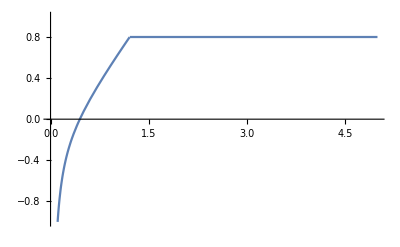

```mathematica
Plot[Vsb[r/0.197,αfinal[[1]],σfinal[[1]],cfinal[[1]]],{r,0,5},PlotRange->{-1,1}]
```

#### Verification

```mathematica
bbswavemass[α_,σ_,c_]:=2mb + NDEigenvalues[{-1/mb Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
bbpwavemass[α_,σ_,c_]:=2mb+NDEigenvalues[{-1/mb Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x]+Veff[x,1,μb]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
bbswavePDG-bbswavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{0.0000440532,0.0000546317,0.0000510613,0.0101638}

```mathematica
bbpwavePDG-bbpwavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{-0.0429899,-0.0207082,-0.000464073}

### Charmonium Fit

```mathematica
ccswavePDG={{3.0969,0.000006},{3.686097,0.0000025}};
ccswavePDG1={3.0969};
```

```mathematica
ccswavemass1[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
mcfinal=m/.Quiet[FindRoot[ccswavemass1[m]==ccswavePDG1,{m,mc}]]
```

1.46919

```mathematica
ccswavemass[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
ccpwavemass[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x]+Veff[x,1,m/2]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ccswavemass[mcfinal]
```

{3.0969,3.66316}

```mathematica
ccpwavemass[mcfinal]
```

{3.50788,3.77448}

```mathematica
ccfinal=NDEigensystem[{-1/mcfinal Laplacian[u[x],{x}]+Vsb[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
2mcfinal +ccfinal[[1]]
```

{3.0969,3.66315}

```mathematica
EMfactor=((2mcfinal +ccfinal[[1,2]]) (ccfinal[[2,1]][10^-100])/10^-100)^2/((2mcfinal +ccfinal[[1,1]])(ccfinal[[2,2]][10^-100])/10^-100)^2
```

2.50781